```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,28000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
Timing[tr[0.515,0.0001,0.267,0,7]]
```

{3.73829,2.}

```mathematica
Import["3impdft.dat"][[13;;102]]
```

{{-0.68,0.878687},{-0.67,0.892918},{-0.66,0.908596},{-0.65,0.930284},{-0.64,1.28518},{-0.63,1.32331},{-0.62,1.38112},{-0.61,1.45267},{-0.6,1.49321},{-0.59,1.53652},{-0.58,1.57096},{-0.57,1.60712},{-0.56,1.62925},{-0.55,1.65677},{-0.54,1.67549},{-0.53,1.69186},{-0.52,1.70508},{-0.51,1.73679},{-0.5,1.75875},{-0.49,1.79138},{-0.48,1.83198},{-0.47,1.84239},{-0.46,1.816},{-0.45,1.91069},{-0.44,1.97761},{-0.43,2.02947},{-0.42,2.06813},{-0.41,2.10959},{-0.4,2.1375},{-0.39,2.15787},{-0.38,2.19319},{-0.37,2.22174},{-0.36,2.2178},{-0.35,2.27328},{-0.34,2.2633},{-0.33,2.29563},{-0.32,2.29973},{-0.31,2.34699},{-0.3,2.34143},{-0.29,2.34025},{-0.28,2.36232},{-0.27,2.37674},{-0.26,2.2919},{-0.25,2.05744},{-0.24,1.5297},{-0.23,0.97994},{-0.22,0.890432},{-0.21,0.837658},{-0.2,0.763863},{-0.19,0.757484},{-0.18,0.890811},{-0.17,0.982629},{-0.16,1.04361},{-0.15,1.04196},{-0.14,1.01607},{-0.13,0.938773},{-0.12,0.769124},{-0.11,0.634991},{-0.1,0.432193},{-0.09,0.549705},{-0.08,0.553504},{-0.07,0.509074},{-0.06,0.000364016},{-0.05,0.0000219466},{-0.04,9.21937×10^-6},{-0.03,5.8566×10^-6},{-0.02,4.61937×10^-6},{-0.01,4.00942×10^-6},{0.,3.92628×10^-6},{0.01,4.05764×10^-6},{0.02,4.60969×10^-6},{0.03,5.87564×10^-6},{0.04,9.14247×10^-6},{0.05,0.0000218355},{0.06,0.000352349},{0.07,0.675149},{0.08,0.778192},{0.09,0.818736},{0.1,0.836105},{0.11,0.786933},{0.12,1.08603},{0.13,1.33112},{0.14,1.43586},{0.15,1.5102},{0.16,1.5526},{0.17,1.61337},{0.18,1.63531},{0.19,1.67524},{0.2,1.69298},{0.21,1.7362}}

```mathematica
Dimensions[%68]
```

{451,2}

```mathematica
Table[{x,Interpolation[Import["3impdft.dat"][[13;;103]]][x]},{x,Range[-0.68,0.22,0.89/445]}][[;;446]]
```

{{-0.68,0.878687},{-0.678,0.881637},{-0.676,0.884498},{-0.674,0.887307},{-0.672,0.890102},{-0.67,0.892918},{-0.668,0.895792},{-0.666,0.89876},{-0.664,0.901859},{-0.662,0.905126},{-0.66,0.908596},{-0.658,0.901982},{-0.656,0.898227},{-0.654,0.899947},{-0.652,0.90976},{-0.65,0.930284},{-0.648,0.995406},{-0.646,1.06866},{-0.644,1.14484},{-0.642,1.21874},{-0.64,1.28518},{-0.638,1.30738},{-0.636,1.3196},{-0.634,1.32454},{-0.632,1.32488},{-0.63,1.32331},{-0.628,1.33349},{-0.626,1.34441},{-0.624,1.35601},{-0.622,1.36827},{-0.62,1.38112},{-0.618,1.39576},{-0.616,1.4106},{-0.614,1.42526},{-0.612,1.43941},{-0.61,1.45267},{-0.608,1.46218},{-0.606,1.47071},{-0.604,1.47855},{-0.602,1.48596},{-0.6,1.49321},{-0.598,1.50202},{-0.596,1.51085},{-0.594,1.51961},{-0.592,1.52819},{-0.59,1.53652},{-0.588,1.54378},{-0.586,1.55077},{-0.584,1.55757},{-0.582,1.56427},{-0.58,1.57096},{-0.578,1.57855},{-0.576,1.5861},{-0.574,1.59346},{-0.572,1.60051},{-0.57,1.60712},{-0.568,1.61205},{-0.566,1.61657},{-0.564,1.62084},{-0.562,1.62501},{-0.56,1.62925},{-0.558,1.63477},{-0.556,1.6404},{-0.554,1.64602},{-0.552,1.65151},{-0.55,1.65677},{-0.548,1.66101},{-0.546,1.66495},{-0.544,1.66864},{-0.542,1.67214},{-0.54,1.67549},{-0.538,1.67898},{-0.536,1.68237},{-0.534,1.68565},{-0.532,1.68882},{-0.53,1.69186},{-0.528,1.69407},{-0.526,1.69632},{-0.524,1.69879},{-0.522,1.70165},{-0.52,1.70508},{-0.518,1.71085},{-0.516,1.71713},{-0.514,1.72369},{-0.512,1.73032},{-0.51,1.73679},{-0.508,1.74131},{-0.506,1.7456},{-0.504,1.74983},{-0.502,1.75416},{-0.5,1.75875},{-0.498,1.76451},{-0.496,1.77067},{-0.494,1.77722},{-0.492,1.78413},{-0.49,1.79138},{-0.488,1.80008},{-0.486,1.8088},{-0.484,1.81723},{-0.482,1.82505},{-0.48,1.83198},{-0.478,1.83669},{-0.476,1.84014},{-0.474,1.84227},{-0.472,1.84304},{-0.47,1.84239},{-0.468,1.835},{-0.466,1.82741},{-0.464,1.82087},{-0.462,1.81665},{-0.46,1.816},{-0.458,1.83002},{-0.456,1.84769},{-0.454,1.86781},{-0.452,1.88921},{-0.45,1.91069},{-0.448,1.92589},{-0.446,1.94008},{-0.444,1.95336},{-0.442,1.96584},{-0.44,1.97761},{-0.438,1.98912},{-0.436,2.00005},{-0.434,2.01041},{-0.432,2.02021},{-0.43,2.02947},{-0.428,2.03774},{-0.426,2.04562},{-0.424,2.05323},{-0.422,2.06069},{-0.42,2.06813},{-0.418,2.07672},{-0.416,2.0853},{-0.414,2.09372},{-0.412,2.10186},{-0.41,2.10959},{-0.408,2.11606},{-0.406,2.12204},{-0.404,2.12757},{-0.402,2.13271},{-0.4,2.1375},{-0.398,2.14145},{-0.396,2.14529},{-0.394,2.14918},{-0.392,2.15332},{-0.39,2.15787},{-0.388,2.16443},{-0.386,2.17142},{-0.384,2.17865},{-0.382,2.18597},{-0.38,2.19319},{-0.378,2.20026},{-0.376,2.20686},{-0.374,2.21278},{-0.372,2.21781},{-0.37,2.22174},{-0.368,2.22061},{-0.366,2.21892},{-0.364,2.2174},{-0.362,2.21678},{-0.36,2.2178},{-0.358,2.22814},{-0.356,2.23986},{-0.354,2.25195},{-0.352,2.26343},{-0.35,2.27328},{-0.348,2.27308},{-0.346,2.27111},{-0.344,2.26825},{-0.342,2.26536},{-0.34,2.2633},{-0.338,2.26864},{-0.336,2.27511},{-0.334,2.28214},{-0.332,2.28917},{-0.33,2.29563},{-0.328,2.29643},{-0.326,2.29666},{-0.324,2.29691},{-0.322,2.29774},{-0.32,2.29973},{-0.318,2.3088},{-0.316,2.31883},{-0.314,2.32905},{-0.312,2.33869},{-0.31,2.34699},{-0.308,2.34827},{-0.306,2.3479},{-0.304,2.34633},{-0.302,2.34402},{-0.3,2.34143},{-0.298,2.34024},{-0.296,2.33937},{-0.294,2.33898},{-0.292,2.33923},{-0.29,2.34025},{-0.288,2.34379},{-0.286,2.34801},{-0.284,2.35267},{-0.282,2.35752},{-0.28,2.36232},{-0.278,2.36874},{-0.276,2.37413},{-0.274,2.37775},{-0.272,2.37887},{-0.27,2.37674},{-0.268,2.36933},{-0.266,2.35754},{-0.264,2.34097},{-0.262,2.31923},{-0.26,2.2919},{-0.258,2.26158},{-0.256,2.22412},{-0.254,2.17837},{-0.252,2.1232},{-0.25,2.05744},{-0.248,1.96667},{-0.246,1.86635},{-0.244,1.75863},{-0.242,1.64569},{-0.24,1.5297},{-0.238,1.40608},{-0.236,1.28543},{-0.234,1.17162},{-0.232,1.0685},{-0.23,0.97994},{-0.228,0.938771},{-0.226,0.912623},{-0.224,0.89811},{-0.222,0.891842},{-0.22,0.890432},{-0.218,0.878787},{-0.216,0.868149},{-0.214,0.858056},{-0.212,0.848047},{-0.21,0.837658},{-0.208,0.821751},{-0.206,0.80571},{-0.204,0.790244},{-0.202,0.776059},{-0.2,0.763863},{-0.198,0.754881},{-0.196,0.749173},{-0.194,0.747319},{-0.192,0.749897},{-0.19,0.757484},{-0.188,0.778772},{-0.186,0.804198},{-0.184,0.832313},{-0.182,0.861667},{-0.18,0.890811},{-0.178,0.912153},{-0.176,0.931921},{-0.174,0.950199},{-0.172,0.967073},{-0.17,0.982629},{-0.168,0.99831},{-0.166,1.0125},{-0.164,1.02495},{-0.162,1.03541},{-0.16,1.04361},{-0.158,1.04706},{-0.156,1.04832},{-0.154,1.04768},{-0.152,1.04546},{-0.15,1.04196},{-0.148,1.03959},{-0.146,1.03603},{-0.144,1.03107},{-0.142,1.02449},{-0.14,1.01607},{-0.138,1.00603},{-0.136,0.993612},{-0.134,0.978481},{-0.132,0.96031},{-0.13,0.938773},{-0.128,0.90814},{-0.126,0.874835},{-0.124,0.839882},{-0.122,0.804304},{-0.12,0.769124},{-0.118,0.74279},{-0.116,0.717043},{-0.114,0.69105},{-0.112,0.663977},{-0.11,0.634991},{-0.108,0.587478},{-0.106,0.540329},{-0.104,0.496658},{-0.102,0.459575},{-0.1,0.432193},{-0.098,0.44396},{-0.096,0.465066},{-0.094,0.49204},{-0.092,0.521411},{-0.09,0.549705},{-0.088,0.557466},{-0.086,0.561203},{-0.084,0.561439},{-0.082,0.558698},{-0.08,0.553504},{-0.078,0.56179},{-0.076,0.564818},{-0.074,0.559261},{-0.072,0.541788},{-0.07,0.509074},{-0.068,0.413349},{-0.066,0.306835},{-0.064,0.197312},{-0.062,0.0925612},{-0.06,0.000364016},{-0.058,-0.0241166},{-0.056,-0.0323268},{-0.054,-0.0283309},{-0.052,-0.0161932},{-0.05,0.0000219466},{-0.048,3.29309×10^-6},{-0.046,-4.74657×10^-6},{-0.044,-4.7322×10^-6},{-0.042,7.76388×10^-7},{-0.04,9.21937×10^-6},{-0.038,8.02931×10^-6},{-0.036,7.15591×10^-6},{-0.034,6.54126×10^-6},{-0.032,6.12747×10^-6},{-0.03,5.8566×10^-6},{-0.028,5.48706×10^-6},{-0.026,5.19055×10^-6},{-0.024,4.95509×10^-6},{-0.022,4.76869×10^-6},{-0.02,4.61937×10^-6},{-0.018,4.45041×10^-6},{-0.016,4.30574×10^-6},{-0.014,4.18456×10^-6},{-0.012,4.08605×10^-6},{-0.01,4.00942×10^-6},{-0.008,3.96064×10^-6},{-0.006,3.93044×10^-6},{-0.004,3.91631×10^-6},{-0.002,3.91575×10^-6},{0.,3.92628×10^-6},{0.002,3.92879×10^-6},{0.004,3.94154×10^-6},{0.006,3.96616×10^-6},{0.008,4.00431×10^-6},{0.01,4.05764×10^-6},{0.012,4.12501×10^-6},{0.014,4.21156×10^-6},{0.016,4.31962×10^-6},{0.018,4.45155×10^-6},{0.02,4.60969×10^-6},{0.022,4.76459×10^-6},{0.024,4.95833×10^-6},{0.026,5.20122×10^-6},{0.028,5.50356×10^-6},{0.03,5.87564×10^-6},{0.032,6.13132×10^-6},{0.034,6.52644×10^-6},{0.036,7.12041×10^-6},{0.038,7.97262×10^-6},{0.04,9.14247×10^-6},{0.042,1.05836×10^-6},{0.044,-4.18154×10^-6},{0.046,-4.11009×10^-6},{0.048,3.73987×10^-6},{0.05,0.0000218355},{0.052,-0.0215102},{0.054,-0.0376364},{0.056,-0.0429635},{0.058,-0.0320983},{0.06,0.000352349},{0.062,0.121233},{0.064,0.259123},{0.066,0.404052},{0.068,0.546051},{0.07,0.675149},{0.072,0.725201},{0.074,0.756458},{0.076,0.772993},{0.078,0.778879},{0.08,0.778192},{0.082,0.790042},{0.084,0.799707},{0.086,0.807502},{0.088,0.81374},{0.09,0.818736},{0.092,0.825452},{0.094,0.830893},{0.096,0.834714},{0.098,0.836567},{0.1,0.836105},{0.102,0.81832},{0.104,0.801192},{0.106,0.788039},{0.108,0.78218},{0.11,0.786933},{0.112,0.831763},{0.114,0.887306},{0.116,0.950344},{0.118,1.01766},{0.12,1.08603},{0.122,1.14213},{0.124,1.19538},{0.126,1.24509},{0.128,1.29057},{0.13,1.33112},{0.132,1.35978},{0.134,1.3837},{0.136,1.40377},{0.138,1.42086},{0.14,1.43586},{0.142,1.45321},{0.144,1.46933},{0.146,1.48421},{0.148,1.49784},{0.15,1.5102},{0.152,1.51963},{0.154,1.52818},{0.156,1.53626},{0.158,1.54426},{0.16,1.5526},{0.162,1.56512},{0.164,1.57791},{0.166,1.59052},{0.168,1.6025},{0.17,1.61337},{0.172,1.61905},{0.174,1.62362},{0.176,1.62756},{0.178,1.6313},{0.18,1.63531},{0.182,1.64314},{0.184,1.65137},{0.186,1.65968},{0.188,1.66774},{0.19,1.67524},{0.192,1.67903},{0.194,1.68233},{0.196,1.6855},{0.198,1.68892},{0.2,1.69298},{0.202,1.70021},{0.204,1.7083},{0.206,1.7171},{0.208,1.72645},{0.21,1.7362}}

```mathematica
NIntegrate[Interpolation[Transpose[Join[{Transpose[Table[{x,Interpolation[Import["10impdft.dat"][[13;;103]]][x]},{x,Range[-0.68,0.22,0.89/445]}][[;;446]]][[1]]},{Abs[Transpose[Table[{Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[1]]+0.372-0.06,Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[2]]/2},{x,1,446}]][[2]]-Transpose[Table[{x,Interpolation[Import["10impdft.dat"][[13;;103]]][x]},{x,Range[-0.68,0.22,0.89/445]}][[;;446]]][[2]]]}]]][x],{x,-0.68,-0.2}]
```

0.28

```mathematica
NIntegrate[Interpolation[Transpose[Join[{Transpose[Table[{x,Interpolation[Import["3impdft.dat"][[13;;103]]][x]},{x,Range[-0.68,0.22,0.89/445]}][[;;446]]][[1]]},{Abs[Transpose[Table[{Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[1]]+0.372-0.06,Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[2]]/2},{x,1,446}]][[2]]-Transpose[Table[{x,Interpolation[Import["3impdft.dat"][[13;;103]]][x]},{x,Range[-0.68,0.22,0.89/445]}][[;;446]]][[2]]]}]]][x],{x,-0.680,-0.2}]
```

0.194343

```mathematica
NIntegrate[Interpolation[Transpose[Join[{Transpose[Table[{x,Interpolation[Import["1impdft.dat"]][x]},{x,Range[-0.68,0.20,0.89/445]}][[;;446]]][[1]]},{Abs[Transpose[Table[{Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[1]]+0.372-0.06,Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[2]]/2},{x,1,446}]][[2]]-Transpose[Table[{x,Interpolation[Import["1impdft.dat"]][x]},{x,Range[-0.68,0.20,0.89/445]}][[;;446]]][[2]]]}]]][x],{x,-0.68,-0.2}]
```

Part::take: Cannot take positions 1 through 446 in {{-0.68,0.953976},{-0.678,0.954662},{-0.676,0.955538},{-0.674,0.956587},{-0.672,0.957791},{-0.67,0.959133},«39»,{-0.59,1.81754},{-0.588,1.81946},{-0.586,1.82123},{-0.584,1.82298},{-0.582,1.82488},«391»}.

Part::partw: Part 2 of Transpose[{{-0.68,0.953976},{-0.678,0.954662},{-0.676,0.955538},{-0.674,0.956587},{-0.672,0.957791},{-0.67,0.959133},«40»,{-0.588,1.81946},{-0.586,1.82123},{-0.584,1.82298},{-0.582,1.82488},«391»}⟦1;;446⟧] does not exist.

Transpose::nmtx: The first two levels of {{{-0.68,0.953976},{-0.678,0.954662},{-0.676,0.955538},{-0.674,0.956587},{-0.672,0.957791},{-0.67,0.959133},«40»,{-0.588,1.81946},{-0.586,1.82123},{-0.584,1.82298},{-0.582,1.82488},«391»}⟦1;;446⟧,{Abs[1.57125-«1»],«49»,«396»}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{{-0.68,0.953976},{-0.678,0.954662},{-0.676,0.955538},{-0.674,0.956587},{-0.672,0.957791},{-0.67,0.959133},«40»,{-0.588,1.81946},{-0.586,1.82123},{-0.584,1.82298},{-0.582,1.82488},«391»}⟦1;;446⟧,{Abs[«1»],«49»,«396»}}] does not contain a list of data and coordinates.

NIntegrate::inumr: The integrand Interpolation[Transpose[{{{-0.68,0.953976},{-0.678,0.954662},{-0.676,0.955538},{-0.674,0.956587},{-0.672,0.957791},{-0.67,0.959133},«40»,{-0.588,1.81946},{-0.586,1.82123},{-0.584,1.82298},{-0.582,1.82488},«391»}⟦1;;446⟧,{«1»}}]][x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-17/25,-1/5}}.

NIntegrate[Interpolation[Transpose[Join[{Transpose[Table[{x,Interpolation[Import[1impdft.dat]][x]},{x,Range[-0.68,0.2,0.89/445]}]⟦1;;446⟧]⟦1⟧},{Abs[Transpose[Table[{Import[/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat]⟦x⟧⟦1⟧+0.372-0.06,1/2 Import[/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat]⟦x⟧⟦2⟧},{x,1,446}]]⟦2⟧-Transpose[Table[{x,Interpolation[Import[1impdft.dat]][x]},{x,Range[-0.68,0.2,0.89/445]}]⟦1;;446⟧]⟦2⟧]}]]][x],{x,-0.68,-0.2}]

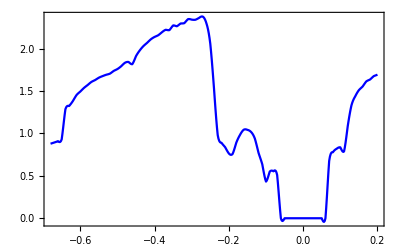

```mathematica
ListPlot[Table[{x,Interpolation[Import["3impdft.dat"][[13;;102]]][x]},{x,Range[-0.68,0.2,0.89/445]}],Joined->True,PlotStyle->Blue,Frame->True]
```

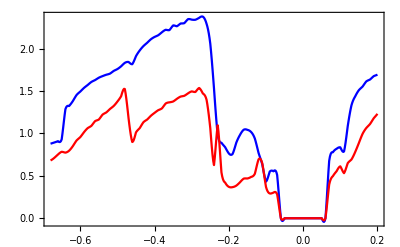

```mathematica
Show[%59,%58]
```

```mathematica
data1:=data1=Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"]
```

```mathematica
z1:=z1=Table[{Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[1]]+0.372-0.06,Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[2]]/2},{x,1,446}]
```

```mathematica
Clear[z1]
```

```mathematica
z1[[1]]
```

{-0.688,1.57125}

```mathematica
Dimensions[z1]
```

{446,2}

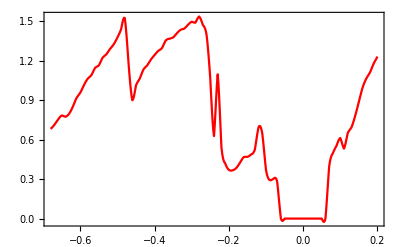

```mathematica
ListLinePlot[Table[{x,Interpolation[Import["10impdft.dat"][[13;;102]]][x]},{x,Range[-0.68,0.2,0.89/445]}],PlotStyle->Red,Frame->True]
```

```mathematica
misfit[ϵ1_,x_,y_]:=Module[{},υ=Module[{},
(*ρ1:=Log[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Log[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp3.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];ρ3:=Log[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp4.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];ρ4:=Log[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9,ρ10*)(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
Transpose[Join[{Transpose[Table[{x,Interpolation[Import["3impdft.dat"][[13;;103]]][x]},{x,Range[-0.68,0.22,0.89/445]}][[;;446]]][[1]]},{Abs[Transpose[Table[{Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[1]]+0.372-0.06,Import["/home/shardulmukim/PhD/fwi/DFT/7AGNR/testN0.0024small.dat"][[x]][[2]]/2},{x,1,446}]][[2]]-Transpose[Table[{x,Interpolation[Import["3impdft.dat"][[13;;103]]][x]},{x,Range[-0.68,0.22,0.89/445]}][[;;446]]][[2]]]}]]
```

{{-0.68,0.69256},{-0.678,0.492674},{-0.676,0.40099},{-0.674,0.575732},{-0.672,0.741382},{-0.67,0.565699},{-0.668,0.520773},{-0.666,0.779236},{-0.664,0.144214},{-0.662,0.217306},{-0.66,0.0877799},{-0.658,0.0851256},{-0.656,0.0549995},{-0.654,0.0305684},{-0.652,0.302194},{-0.65,0.0362931},{-0.648,0.107138},{-0.646,0.0868002},{-0.644,0.00544221},{-0.642,0.41196},{-0.64,0.427812},{-0.638,0.664412},{-0.636,0.0137015},{-0.634,0.26732},{-0.632,0.230458},{-0.63,0.139923},{-0.628,0.369563},{-0.626,0.525878},{-0.624,0.495941},{-0.622,0.345683},{-0.62,0.160377},{-0.618,0.466883},{-0.616,0.208289},{-0.614,0.0722528},{-0.612,0.329768},{-0.61,0.688023},{-0.608,0.346536},{-0.606,0.191448},{-0.604,0.0788836},{-0.602,0.289466},{-0.6,0.0996986},{-0.598,0.113352},{-0.596,0.47786},{-0.594,0.154692},{-0.592,0.00496073},{-0.59,0.567853},{-0.588,0.545554},{-0.586,0.721593},{-0.584,0.657807},{-0.582,0.672984},{-0.58,0.177279},{-0.578,0.66168},{-0.576,0.866351},{-0.574,0.82793},{-0.572,0.832004},{-0.57,0.68246},{-0.568,0.191773},{-0.566,0.391056},{-0.564,0.0680399},{-0.562,0.072369},{-0.56,0.135616},{-0.558,0.871075},{-0.556,0.162995},{-0.554,0.432062},{-0.552,0.756571},{-0.55,0.262529},{-0.548,0.264906},{-0.546,0.399748},{-0.544,0.156017},{-0.542,0.708305},{-0.54,0.594534},{-0.538,0.0833342},{-0.536,0.0149946},{-0.534,0.0218104},{-0.532,0.986847},{-0.53,0.786479},{-0.528,0.992893},{-0.526,0.2161},{-0.524,0.115542},{-0.522,0.32104},{-0.52,0.134561},{-0.518,0.336422},{-0.516,0.15147},{-0.514,0.0807715},{-0.512,0.435224},{-0.51,0.141861},{-0.508,0.697835},{-0.506,0.215708},{-0.504,0.195362},{-0.502,0.731633},{-0.5,0.639885},{-0.498,0.811579},{-0.496,1.17802},{-0.494,0.445987},{-0.492,0.976626},{-0.49,0.856353},{-0.488,0.651434},{-0.486,0.652115},{-0.484,0.578827},{-0.482,0.0717201},{-0.48,0.337714},{-0.478,0.0845611},{-0.476,0.253734},{-0.474,0.735708},{-0.472,0.513147},{-0.47,0.970895},{-0.468,0.326201},{-0.466,0.140974},{-0.464,0.0874718},{-0.462,0.0217377},{-0.46,0.512448},{-0.458,0.291957},{-0.456,0.0561112},{-0.454,0.0254614},{-0.452,0.262091},{-0.45,0.87301},{-0.448,0.656558},{-0.446,0.766773},{-0.444,0.099232},{-0.442,0.161863},{-0.44,0.521179},{-0.438,0.268279},{-0.436,0.433471},{-0.434,0.365394},{-0.432,0.105163},{-0.43,0.341865},{-0.428,0.182779},{-0.426,0.568699},{-0.424,0.106055},{-0.422,0.0306121},{-0.42,0.58504},{-0.418,0.540335},{-0.416,0.15169},{-0.414,0.300986},{-0.412,0.13274},{-0.41,0.934869},{-0.408,0.112972},{-0.406,0.106076},{-0.404,0.247258},{-0.402,0.192366},{-0.4,0.132514},{-0.398,0.103944},{-0.396,0.0858308},{-0.394,0.351242},{-0.392,0.265701},{-0.39,0.628633},{-0.388,0.931955},{-0.386,0.280963},{-0.384,0.411268},{-0.382,0.89311},{-0.38,0.722628},{-0.378,0.458816},{-0.376,0.376909},{-0.374,0.00738768},{-0.372,0.171443},{-0.37,0.564728},{-0.368,0.38626},{-0.366,0.441024},{-0.364,0.803308},{-0.362,0.859325},{-0.36,0.753419},{-0.358,0.299623},{-0.356,0.201422},{-0.354,0.228307},{-0.352,0.16789},{-0.35,0.0470322},{-0.348,0.0585626},{-0.346,0.42872},{-0.344,0.252618},{-0.342,0.505521},{-0.34,0.474625},{-0.338,0.643572},{-0.336,0.529171},{-0.334,0.369414},{-0.332,0.315817},{-0.33,0.205038},{-0.328,0.528069},{-0.326,0.300437},{-0.324,0.100016},{-0.322,0.20523},{-0.32,0.280274},{-0.318,0.00733473},{-0.316,0.987231},{-0.314,0.699368},{-0.312,0.327386},{-0.31,0.461775},{-0.308,0.275849},{-0.306,0.580574},{-0.304,0.0584157},{-0.302,0.334869},{-0.3,0.557719},{-0.298,0.326909},{-0.296,0.0377216},{-0.294,0.441991},{-0.292,1.01105},{-0.29,1.10434},{-0.288,1.11387},{-0.286,0.0603963},{-0.284,0.036066},{-0.282,0.150405},{-0.28,0.385693},{-0.278,0.672674},{-0.276,0.693664},{-0.274,0.535742},{-0.272,0.201781},{-0.27,0.184074},{-0.268,0.448662},{-0.266,0.424669},{-0.264,1.07433},{-0.262,0.841597},{-0.26,0.894758},{-0.258,1.04804},{-0.256,0.174518},{-0.254,0.920669},{-0.252,1.43082},{-0.25,0.178103},{-0.248,0.0434321},{-0.246,0.321064},{-0.244,0.471999},{-0.242,0.0133753},{-0.24,0.3992},{-0.238,0.382655},{-0.236,0.336945},{-0.234,0.145295},{-0.232,0.0656111},{-0.23,0.0674854},{-0.228,0.21564},{-0.226,0.413069},{-0.224,0.00489752},{-0.222,0.297411},{-0.22,0.0867634},{-0.218,0.145786},{-0.216,0.0309376},{-0.214,0.449965},{-0.212,0.504432},{-0.21,0.522589},{-0.208,1.086},{-0.206,1.02756},{-0.204,1.08003},{-0.202,1.45454},{-0.2,0.729373},{-0.198,0.612961},{-0.196,0.527487},{-0.194,0.85972},{-0.192,1.0139},{-0.19,0.932211},{-0.188,0.752262},{-0.186,0.0701514},{-0.184,0.290874},{-0.182,1.40347},{-0.18,0.567891},{-0.178,1.2143},{-0.176,0.985947},{-0.174,0.814926},{-0.172,1.18646},{-0.17,1.12255},{-0.168,0.984108},{-0.166,1.0072},{-0.164,1.10786},{-0.162,1.17833},{-0.16,1.29204},{-0.158,1.27209},{-0.156,1.22239},{-0.154,1.33592},{-0.152,1.44989},{-0.15,1.33537},{-0.148,0.782024},{-0.146,0.776443},{-0.144,0.372275},{-0.142,0.25441},{-0.14,0.341242},{-0.138,0.390304},{-0.136,0.848007},{-0.134,0.710966},{-0.132,0.239628},{-0.13,0.0332055},{-0.128,0.804722},{-0.126,0.824289},{-0.124,0.774986},{-0.122,0.470414},{-0.12,0.290231},{-0.118,0.147316},{-0.116,0.694832},{-0.114,0.778277},{-0.112,0.278923},{-0.11,0.411668},{-0.108,0.423448},{-0.106,0.650319},{-0.104,0.623087},{-0.102,0.638264},{-0.1,0.791627},{-0.098,0.786633},{-0.096,0.27248},{-0.094,0.0581571},{-0.092,0.122483},{-0.09,0.094917},{-0.088,0.301992},{-0.086,0.283645},{-0.084,0.0376394},{-0.082,0.189974},{-0.08,0.038131},{-0.078,0.0907952},{-0.076,0.0989019},{-0.074,0.0560051},{-0.072,0.0299695},{-0.07,0.401974},{-0.068,0.00180898},{-0.066,0.0988911},{-0.064,0.253186},{-0.062,0.0953079},{-0.06,0.237515},{-0.058,0.0241166},{-0.056,0.0323268},{-0.054,0.0283309},{-0.052,0.0161932},{-0.05,0.0000219466},{-0.048,3.29309×10^-6},{-0.046,4.74657×10^-6},{-0.044,4.7322×10^-6},{-0.042,7.76388×10^-7},{-0.04,9.21937×10^-6},{-0.038,8.02931×10^-6},{-0.036,7.15591×10^-6},{-0.034,6.54126×10^-6},{-0.032,6.12747×10^-6},{-0.03,5.8566×10^-6},{-0.028,5.48706×10^-6},{-0.026,5.19055×10^-6},{-0.024,4.95509×10^-6},{-0.022,4.76869×10^-6},{-0.02,4.61937×10^-6},{-0.018,4.45041×10^-6},{-0.016,4.30574×10^-6},{-0.014,4.18456×10^-6},{-0.012,4.08605×10^-6},{-0.01,4.00942×10^-6},{-0.008,3.96064×10^-6},{-0.006,3.93044×10^-6},{-0.004,3.91631×10^-6},{-0.002,3.91575×10^-6},{0.,3.92628×10^-6},{0.002,3.92879×10^-6},{0.004,3.94154×10^-6},{0.006,3.96616×10^-6},{0.008,4.00431×10^-6},{0.01,4.05764×10^-6},{0.012,4.12501×10^-6},{0.014,4.21156×10^-6},{0.016,4.31962×10^-6},{0.018,4.45155×10^-6},{0.02,4.60969×10^-6},{0.022,4.76459×10^-6},{0.024,4.95833×10^-6},{0.026,5.20122×10^-6},{0.028,5.50356×10^-6},{0.03,5.87564×10^-6},{0.032,6.13132×10^-6},{0.034,6.52644×10^-6},{0.036,7.12041×10^-6},{0.038,7.97262×10^-6},{0.04,9.14247×10^-6},{0.042,1.05836×10^-6},{0.044,4.18154×10^-6},{0.046,4.11009×10^-6},{0.048,3.73987×10^-6},{0.05,0.0000218355},{0.052,0.0215102},{0.054,0.0376364},{0.056,0.0429635},{0.058,0.0320983},{0.06,0.000352349},{0.062,0.121233},{0.064,0.20608},{0.066,0.16561},{0.068,0.209737},{0.07,0.648812},{0.072,0.723012},{0.074,0.682946},{0.076,0.478816},{0.078,0.77798},{0.08,0.74898},{0.082,0.663984},{0.084,0.769524},{0.086,0.804223},{0.088,0.804531},{0.09,0.73282},{0.092,0.787996},{0.094,0.437867},{0.096,0.602821},{0.098,0.488716},{0.1,0.728448},{0.102,0.807904},{0.104,0.789184},{0.106,0.781452},{0.108,0.365314},{0.11,0.688002},{0.112,0.361926},{0.114,0.0611836},{0.116,0.56919},{0.118,0.891751},{0.12,0.125149},{0.122,0.578411},{0.124,0.118367},{0.126,0.166571},{0.128,0.190031},{0.13,0.20029},{0.132,0.202974},{0.134,0.127465},{0.136,0.122873},{0.138,0.303867},{0.14,0.0569623},{0.142,0.0993734},{0.144,0.341047},{0.146,0.0177815},{0.148,0.33389},{0.15,0.307171},{0.152,0.16654},{0.154,0.121543},{0.156,0.0151263},{0.158,0.233921},{0.16,0.124191},{0.162,0.389015},{0.164,0.141435},{0.166,0.271872},{0.168,0.238834},{0.17,0.175035},{0.172,0.293014},{0.174,0.281871},{0.176,0.212722},{0.178,0.176446},{0.18,0.0338521},{0.182,0.383808},{0.184,0.754436},{0.186,0.672124},{0.188,0.229211},{0.19,0.0110295},{0.192,0.00340824},{0.194,0.150805},{0.196,0.468239},{0.198,0.117687},{0.2,0.133926},{0.202,0.181756},{0.204,0.01383},{0.206,0.356014},{0.208,0.456034},{0.21,0.108213}}

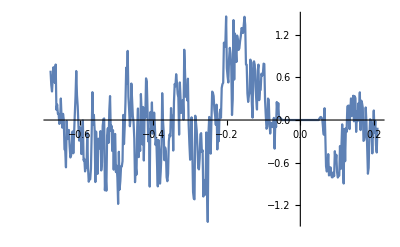

```mathematica
ListPlot[%89,Joined->True]
```